# ME314 - Final Project Gerik Zatorski

```mathematica
Quit[];
```

## Kinematics of Shot

```mathematica
ClearAll["Global`*"]

(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

(* Conversions *)
FtToM=0.3048;

(* Court Dimensions *)
BaselineToBackboard=4*FtToM;
BaselineToFoulLine=19*FtToM;
BaselineToThreePoint=22*FtToM;
BackboardToRim=6/12*FtToM; (* to outer edge of rim *)
RimThickness =5/8/12*FtToM;
RimDiameter=18/12*FtToM; (* TODO: I have assumed this center to center of steel *)
BackboardBaseHeight=9*FtToM;
GroundToRim=10*FtToM;(* ground to top of rim *)
GroundToBackboard=9*FtToM;
BackboardHeight=4*FtToM;

(* Unused Dimensions *)
BaselineToRimCenter=63/12*FtToM;

(* 2D Static Coordinates *)
coordFoulLine={-BaselineToFoulLine,0};
coordThreePtLine = {-BaselineToThreePoint,0};
coordBackboardBase={-BaselineToBackboard,GroundToBackboard};
coordBackboardTop={-BaselineToBackboard,GroundToBackboard+BackboardHeight};
coordRimBack={-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2};
coordRimFront={-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2};

(* My dimensions (links in inches) *)
Lfoot=0.3048*10/12;
Lshin=0.3048*21/12;
Lthigh=0.3048*21/12;
Ltorso=0.3048*20/12;
Lbicep=0.3048*11/12;
Lforearm=0.3048*12/12;
Lhand=0.3048*8.5/12;

(* Joint Frame Transformations *)
gtoe=g[BaselineToFoulLine,0,0].g[0,0,θtoe[t]];
gankle=gtoe.g[Lfoot,0,0].g[0,0,θankle[t]]; (* TODO: will this angle be less than or greater than Pi? I think less than *)
gknee=gankle.g[Lshin,0,0].g[0,0,θknee[t]]; (* I think this one is will be 0->-Pi *)
ghip=gknee.g[Lthigh,0,0].g[0,0,θhip[t]];
gshoulder=ghip.g[Ltorso,0,0].g[0,0,θshoulder[t]];
gelbow=gshoulder.g[Lbicep,0,0].g[0,0,θelbow[t]];
gwrist=gelbow.g[Lforearm,0,0].g[0,0,θwrist[t]];
gfingertip=gwrist.g[Lhand,0,0];

(* Other Frame Transformations *)
gballbefore=gwrist.g[Lhand/2,rball,0]; (* transformation before ball is released from constraint *)
gline1before=gballbefore.g[-rball,0,0];
gline2before=gballbefore.g[rball,0,0];

(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;

(* Fake Joint Velocities *)
θtoesol=ListInterpolation[Pi/12*{0,5},{0,5/4}][t];
θanklesol=ListInterpolation[{Pi*5/8,Pi*1/8},{0,5/4}][t];
θkneesol=ListInterpolation[{-Pi*1/2,-Pi*1/12},{0,5/4}][t];
θhipsol=ListInterpolation[{Pi/2,Pi*1/10},{0,5/4}][t];
θshouldersol=ListInterpolation[{Pi/2,Pi*1/8},{0,5/4}][t];
θelbowsol=ListInterpolation[{-Pi*1/2,0},{0,5/4}][t];
θwristsol=ListInterpolation[{-Pi*1/2,Pi*4/7},{0,5/4}][t]; (* the actual wrist sol should be delayed and maybe synced with release time *)

(*********************************** Shot Animation ****************************************)
coordtoe[t_]:={gtoe[[1,3]],gtoe[[2,3]]};
coordankle[time_]:=({gankle[[1,3]],gankle[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordknee[time_]:=({gknee[[1,3]],gknee[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordhip[time_]:=({ghip[[1,3]],ghip[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordshoulder[time_]:=({gshoulder[[1,3]],gshoulder[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordelbow[time_]:=({gelbow[[1,3]],gelbow[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordwrist[time_]:=({gwrist[[1,3]],gwrist[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordfingertip[time_]:=({gfingertip[[1,3]],gfingertip[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordballbefore[time_]:=({gballbefore[[1,3]],gballbefore[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordline1before[time_]:=({gline1before[[1,3]],gline1before[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;
coordline2before[time_]:=({gline2before[[1,3]],gline2before[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol})/.t->time;

(* Joint Graphics *)
Graphicsfoot=Line[{coordtoe[t],coordankle[t]}];
Graphicsshin=Line[{coordankle[t],coordknee[t]}];
Graphicsthigh=Line[{coordknee[t],coordhip[t]}];
Graphicstorso=Line[{coordhip[t],coordshoulder[t]}];
Graphicsbicep=Line[{coordshoulder[t],coordelbow[t]}];
Graphicsforearm=Line[{coordelbow[t],coordwrist[t]}];
Graphicshand=Line[{coordwrist[t],coordfingertip[t]}];

(* Other Graphics *)
Graphicsballbefore = Circle[coordballbefore[t],rball];
Graphicsballlinebefore=Line[{coordline1before[t],coordline2before[t]}];

(* Solving for conditions at release *)
trelease=.1;
tr=gballbefore/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol}/.t->trelease;
x1=tr[[1,3]];
y1=tr[[2,3]];
θ1=N[ArcCos[tr[[1,1]]]];
tr1=gballbefore/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol}/.t->(trelease-.01);
tr2=gballbefore/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol}/.t->(trelease+.01);

x1dot=N[(tr2[[1,3]]-tr1[[1,3]])/.02];
y1dot=N[(tr2[[2,3]]-tr1[[2,3]])/.02];
θ1dot=N[(ArcCos[tr2[[1,1]]]-ArcCos[tr1[[1,1]]])/.02];

(* Animations *)

(*graphics = Graphics[{
Black,Graphicsfoot/.t->time,
Black,Graphicsshin/.t->time,
Black,Graphicsthigh/.t->time,
Black,Graphicstorso/.t->time,
Black,Graphicsbicep/.t->time,
Black,Graphicsforearm/.t->time,
Black,Graphicshand/.t->time,
Black,Graphicsballbefore/.t->time,
Black,Graphicsballlinebefore/.t->time
},
PlotRange->{{0,7},{-1,5}},Axes->True];

frames=Table[graphics,{time,0,5/4,0.1}];
anim=ListAnimate[frames,AnimationRate->0.2];
Export["~/Desktop/Shot_Kinematics_Calculate_Conditions_At_Release.gif",frames];

Animate[
Show[
Graphics[{
Black,Graphicsfoot/.t->time,
Black,Graphicsshin/.t->time,
Black,Graphicsthigh/.t->time,
Black,Graphicstorso/.t->time,
Black,Graphicsbicep/.t->time,
Black,Graphicsforearm/.t->time,
Black,Graphicshand/.t->time,
Black,Graphicsballbefore/.t->time,
Black,Graphicsballlinebefore/.t->time
}]
],
{time,0,5/4},
AnimationRunning->False,
AnimationRate->1.0
]*)
```

## Release and Roll -> Launch Initial Conditions

```mathematica
gball=g[x[t],y[t],0].g[0,0,θ[t]];
gline1=gball.g[-rball,0,0];
gline2=gball.g[rball,0,0];

(* Fake Joint Velocities *)
θtoe[t]=ListInterpolation[Pi/12*{0,1,2,3,4,5},{0,5/4}][t];
θankle[t]=ListInterpolation[{Pi*5/8,Pi*1/8},{0,5/4}][t];
θknee[t]=ListInterpolation[{-Pi*1/2,-Pi*1/12},{0,5/4}][t];
θhip[t]=ListInterpolation[{Pi/2,Pi*1/10},{0,5/4}][t];
θshoulder[t]=ListInterpolation[{Pi/2,Pi*1/8},{0,5/4}][t];
θelbow[t]=ListInterpolation[{-Pi*1/2,0},{0,5/4}][t];
θwrist[t]=ListInterpolation[{-Pi*1/2,Pi*4/7},{0,5/4}][t]; (* the actual wrist sol should be delayed and maybe synced with release time *)

(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Non Transformed Lagrangian *)
(*Iball=2/3*m*rball^2;
KE=1/2*m*(xa'[t]^2+ya'[t]^2)+1/2*Iball*θa'[t]^2;
PEa=m*g*ya[t];
La=KEa-PEa;*)

Vball=unhat[Inverse[gball].D[gball,t]];

(* Lagrangian using body velocities (see lecture 23) *)
Iball=DiagonalMatrix[{m,m,J}];
J=1;
KE=1/2*(Vball.Iball).{Vball}ᵀ;
PE=m*grav*y[t];
L =KE-PE;

(* External forces *)

(* Constraints *)
(* ball is tangent to hand *)
(*d1=Distance2D[{gball[[1,3]],gball[[2,3]]},coordwrist[trelease]];
d2=Distance2D[{gball[[1,3]],gball[[2,3]]},coordfingertip[trelease]];
l1=Sqrt[rball^2+d1^2];
l2=Sqrt[rball^2+d2^2];
ϕa=Lhand-(l1+l2);*)
(* ball is tangent to hand using frames (no-slip condition) *)
ballinwristframe=UnHom[Inverse[gwrist].gball.Hom[{0,0}]];
ϕa=First[ballinwristframe]-rball*θ[t]

(* Euler-Lagrange equations VECTORS *)
Eq1=D[D[L,x'[t]],t]-D[L,x[t]]==λa*D[ϕa,x[t]];
Eq2=D[D[L,y'[t]],t]-D[L,y[t]]==λa*D[ϕa,y[t]];
Eq3=D[D[L,θ'[t]],t]-D[L,θ[t]]==λa*D[ϕa,θ[t]];
Eq4=ϕa==0;
ELtemp=Solve[{Eq1&&Eq2&&Eq3&&Eq4},{x''[t],y''[t],θ''[t],λa}];
EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Unconstrainted test *)
(*Eq1=D[D[L,x'[t]],t]-D[L,x[t]]==0;
Eq2=D[D[L,y'[t]],t]-D[L,y[t]]==0;
Eq3=D[D[L,θ'[t]],t]-D[L,θ[t]]==0;
ELtemp=Solve[{Eq1&&Eq2&&Eq3},{x''[t],y''[t],θ''[t]}];
EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};*)

(* Constants *)
grav = 9.8;

(* Initial Condition *)
InitCon={x[trelease]==x1,y[trelease]==y1,θ[trelease]==θ1,x'[trelease]==x1dot,y'[trelease]==y1dot,θ'[trelease]==θ1dot};

(* Numerical Solution *)
tmax =5/4;
sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,trelease,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},WorkingPrecision->30,AccuracyGoal->8,PrecisionGoal->8,MaxSteps->20000
];

xsol=x[t]/.sol;
ysol=y[t]/.sol;
θsol=θ[t]/.sol;

coordball[time_]:=({gball[[1,3]],gball[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordline1[time_]:=({gline1[[1,3]],gline1[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordline2[time_]:=({gline2[[1,3]],gline2[[2,3]]}/.{θtoe[t]->θtoesol,θankle[t]->θanklesol,θknee[t]->θkneesol,θhip[t]->θhipsol,θshoulder[t]->θshouldersol,θelbow[t]->θelbowsol,θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;

Graphicsball = Circle[{coordball[t][[1]][[1]],coordball[t][[2]][[1]]},rball];
Graphicsballline=Line[{{coordline1[t][[1]][[1]],coordline1[t][[2]][[1]]},{coordline2[t][[1]][[1]],coordline2[t][[2]][[1]]}}];

(*Animate[
Show[
Graphics[{
Black,Graphicsfoot/.t->time,
Black,Graphicsshin/.t->time,
Black,Graphicsthigh/.t->time,
Black,Graphicstorso/.t->time,
Black,Graphicsbicep/.t->time,
Black,Graphicsforearm/.t->time,
Black,Graphicshand/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time
}],
PlotRange->{{0,7},{-1,5}},
Axes->True
],
{time,trelease,tmax},
AnimationRunning->False,
AnimationRate->1.0
]

graphics = Graphics[{
Black,Graphicsfoot/.t->time,
Black,Graphicsshin/.t->time,
Black,Graphicsthigh/.t->time,
Black,Graphicstorso/.t->time,
Black,Graphicsbicep/.t->time,
Black,Graphicsforearm/.t->time,
Black,Graphicshand/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time
},PlotRange->{{0,7},{-1,5}},Axes->True]

frames=Table[graphics,{time,trelease,tmax,0.1}];
anim=ListAnimate[frames,AnimationRate->0.2];
Export["~/Desktop/Dropping_The_Ball_Figuratively_Speaking.gif",frames];*)
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

Part::partw: Part 3 of Inverse[9.8[x[t],y[t],0].9.8[0,0,θ[t]]] does not exist.

Part::partw: Part 3 of 0.9.8[0,0,θ[t]]+9.8[x[t],y[t],0].0 does not exist.

Part::partw: Part 3 of Inverse[9.8[x[t],y[t],0.].9.8[0.,0.,θ[t]]] does not exist.

Part::partw: Part 3 of 0..9.8[0.,0.,θ[t]]+9.8[x[t],y[t],0.].0. does not exist.

Part::partw: Part 3 of Inverse[9.8[x[t],y[t],0.].9.8[0.,0.,θ[t]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Inverse[gwrist]-0.121285 θ[t]

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve::ndsv: Cannot find starting value for the variable x.

ReplaceAll::reps: {NDSolve[{x''[t]=={}⟦1,1,2⟧,y''[t]=={}⟦1,2,2⟧,θ''[t]=={}⟦1,3,2⟧,x[trelease]==x1,y[trelease]==y1,θ[trelease]==θ1,x'[trelease]==x1dot,y'[trelease]==y1dot,θ'[trelease]==θ1dot},{x,y,θ},{t,trelease,5/4},Method→{ExplicitRungeKutta,DifferenceOrder→4},WorkingPrecision→30,AccuracyGoal→8,PrecisionGoal→8,MaxSteps→20000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

## Shot Result

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Backboard!

0.890143

Front Rim Impact!

0.987409

-1.11818

-3.90736

Ground Impact

1.44888

Ground Impact

2.82517

Ground Impact

3.9262

Ground Impact

4.80702

Set::shape: Lists {times} and {} are not the same shape.

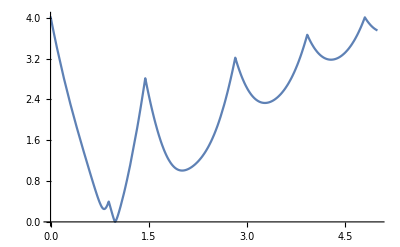

```mathematica
ClearAll["Global`*"]

(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

(* Conversions *)
FtToM=0.3048;

(* Court Dimensions *)
BaselineToBackboard=4*FtToM;
BaselineToFoulLine=19*FtToM;
BaselineToThreePoint=22*FtToM;
BackboardToRim=6/12*FtToM; (* to outer edge of rim *)
RimThickness =5/8/12*FtToM;
RimDiameter=18/12*FtToM; (* TODO: I have assumed this center to center of steel *)
BackboardBaseHeight=9*FtToM;
GroundToRim=10*FtToM;(* ground to top of rim *)
GroundToBackboard=9*FtToM;
BackboardHeight=4*FtToM;

(* Unused Dimensions *)
BaselineToRimCenter=63/12*FtToM;

(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;

(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian *)
Iball=2/3*m*rball^2;
KE=1/2*m*(x'[t]^2+y'[t]^2)+1/2*Iball*θ'[t]^2;
PE=m*g*y[t];
L=KE-PE;

(* Euler-Lagrange equations *)
Eq=(Thread[D[L,qᵀ]-D[D[L,dqᵀ],t]==0]);
ELtemp=Solve[Eq[[1]]&&Eq[[2]]&&Eq[[3]],{y''[t],x''[t],θ''[t]}];
EL={y''[t]==ELtemp[[1,1,2]],x''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Hamiltonian *)
p=D[L,dqᵀ];
H=p.dq-L;

(* Impact Equations - solving for velocities after impact *)
(* Impact with ground *)
ϕ0=y[t]-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ0dq1p)/.(y'[t]->ϕ0dq2p)/.(θ'[t]->ϕ0dq3p))-(D[L,dqᵀ])==λ*D[ϕ0,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ0dq1p)/.(y'[t]->ϕ0dq2p)/.(θ'[t]->ϕ0dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ0dq1p,ϕ0dq2p,ϕ0dq3p,λ}];
ϕ0dq1p=IEq[[1,1,2]]*c;
ϕ0dq2p=IEq[[1,2,2]]*c;
ϕ0dq3p=IEq[[1,3,2]];
(* Impact with backboard *)
ϕ1=x[t]+rball+BaselineToBackboard;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ1dq1p)/.(y'[t]->ϕ1dq2p)/.(θ'[t]->ϕ1dq3p))-(D[L,dqᵀ])==λ*D[ϕ1,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ1dq1p)/.(y'[t]->ϕ1dq2p)/.(θ'[t]->ϕ1dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ1dq1p,ϕ1dq2p,ϕ1dq3p,λ}];
ϕ1dq1p=IEq[[1,1,2]]*c;
ϕ1dq2p=IEq[[1,2,2]]*c;
ϕ1dq3p=IEq[[1,3,2]];
(* Impact with front rim *)
ϕ2=Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2}]-RimThickness/2-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ2dq1p)/.(y'[t]->ϕ2dq2p)/.(θ'[t]->ϕ2dq3p))-(D[L,dqᵀ])==λ*D[ϕ2,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ2dq1p)/.(y'[t]->ϕ2dq2p)/.(θ'[t]->ϕ2dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ2dq1p,ϕ2dq2p,ϕ2dq3p,λ}];
ϕ2dq1p=IEq[[2,1,2]]*c;
ϕ2dq2p=IEq[[2,2,2]]*c;
ϕ2dq3p=IEq[[2,3,2]];
(* Impact with back rim *)
ϕ3=Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2}]-RimThickness/2-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ3dq1p)/.(y'[t]->ϕ3dq2p)/.(θ'[t]->ϕ3dq3p))-(D[L,dqᵀ])==λ*D[ϕ3,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ3dq1p)/.(y'[t]->ϕ3dq2p)/.(θ'[t]->ϕ3dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ3dq1p,ϕ3dq2p,ϕ3dq3p,λ}];
ϕ3dq1p=IEq[[1,1,2]]*c;
ϕ3dq2p=IEq[[1,2,2]]*c;
ϕ3dq3p=IEq[[1,3,2]];

(* Constants *)
g=9.8;
(* Coefficient of Restitution *)
c=0.8;

(* Initial Conditions - TODO: replace these with results from shot dynamics.08.08*)
(* Impacts with backboard, front rim *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==6.5*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* Impacts with backboard, back rim *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==5.5*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* Impacts with backboard, MAYBE front rim back rim *)
InitCon={x[0]==-BaselineToFoulLine,y[0]==5.8*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};
(* Impacts with front rim - short shot *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==4.2*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* over the backboard *)
(*InitCon={x[0]==-BaselineToFoulLine,y[0]==8.3*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)

(* Numerical Solution *)
tmax=5;
newxdot=0;
newydot=0;
newθdot=0;
(* TODO: better options to avoid missing (ex. "back rim" printed when tmax=5, but no change in direction) *)
{sol,{times}}=NDSolve[Join[EL,InitCon,
(* impact with ground *)
{WhenEvent[y[t]-rball==0,{Print["Ground Impact"],end=t,Print[end],newxdot=N[ϕ0dq1p],newydot=N[ϕ0dq2p],newθdot=N[ϕ0dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot},"DetectionMethod"->"Interpolation"]},
(* impact with backboard - TODO: improve y triggers*)
{WhenEvent[x[t]+rball+BaselineToBackboard==0&&y[t]<(BackboardBaseHeight+GroundToBackboard)&&y[t]>BackboardBaseHeight,{Print["Backboard!"],end=t,Print[end],newxdot=N[ϕ1dq1p],newydot=N[ϕ1dq2p],newθdot=N[ϕ1dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot},"DetectionMethod"->"Interpolation"]},
(* impact with front rim *)
{WhenEvent[Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2}]-RimThickness/2-rball==0,{Print["Front Rim Impact!"],end=t,Print[end],newxdot=N[ϕ2dq1p],newydot=N[ϕ2dq2p],newθdot=N[ϕ2dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot,Print[newxdot],Print[newydot]},
"DetectionMethod"->"Interpolation",
"IntegrateEvent"->True,
"LocationMethod"->{"Brent",AccuracyGoal->12,PrecisionGoal->12}]},
(* impact with back rim *)
{WhenEvent[Distance2D[{x[t],y[t]},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2}]-RimThickness/2-rball==0,
{Print["Back Rim Impact!"],end=t,Print[end],newxdot=N[ϕ3dq1p],newydot=N[ϕ3dq2p],newθdot=N[ϕ3dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot,Print[newxdot],Print[newydot]},
"DetectionMethod"->"Interpolation",
"LocationMethod"->{"Brent",AccuracyGoal->12,PrecisionGoal->12}]}
],{x,y,θ},{t,0,tmax}]//Reap;



(*ListPlot[RealExponent[Differences[times]]]*)

xsol=First[x[t]/.sol];
ysol=First[y[t]/.sol];
θsol=First[θ[t]/.sol];

Plot[Distance2D[{xsol,ysol},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2,0}]-RimThickness/2-rball,{t,0,tmax}]

(* Dynamic Graphics *)
BallGraphic=Circle[{xsol,ysol},diameterBall/2];
BallLineGraphic=Line[{{xsol-rball*Cos[θsol],ysol-rball*Sin[θsol]},{xsol+rball*Cos[θsol],ysol+rball*Sin[θsol]}}];

(* Static Graphics *)
FloorGraphic=Line[{{-22*FtToM,0},{0,0}}];
BackboardGraphic=Line[{{-BaselineToBackboard,BackboardBaseHeight},{-BaselineToBackboard,BackboardBaseHeight+GroundToBackboard}}];
FrontRimGraphic=Disk[{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2},RimThickness/2];
BackRimGraphic=Disk[{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},RimThickness/2];
NetFrontGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2},{-BaselineToBackboard-BackboardToRim-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2-.2}}];
NetBackGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2-.2}}];
HitchGraphic=Line[{{-BaselineToBackboard-BackboardToRim-RimThickness/2,GroundToRim-RimThickness/2},{-BaselineToBackboard,GroundToRim-RimThickness/2}}];

(*Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
}],
PlotRange->{{-8,1},{-1,6}},
Axes->True,
ImageSize->Full
],
{time,0,tmax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{1000,800}
]

Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
}],
PlotRange->{{-2.5,-1},{2.5,4.1}},
Axes->True,
ImageSize->Full
],
{time,0,tmax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{800,700}
]

graphics = Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
},PlotRange->{{-8,1},{-1,6}},
Axes->True]

frames=Table[graphics,{time,0,tmax,0.1}];
anim=ListAnimate[frames,AnimationRate->0.4];
Export["~/Desktop/Court_View.gif",frames];

graphics = Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
},
PlotRange->{{-2.5,-1},{2.5,4.1}},Axes->True]

frames=Table[graphics,{time,0,tmax,0.01}];
anim=ListAnimate[frames,AnimationRate->0.4];
Export["~/Desktop/Basket_View.gif",frames];*)
```